Computing the Adjoint Equations given a cost function symbolically

```mathematica
Clear["Global`*"]; (* Fix Bugs here *)
Remove["Global`*"];

Clear[u];
n=20;τ=15;τ1= τ*1.25 ;
nDim = 4;
Δt=τ/n;
xState = {x,xdot,θ,θdot};
λ = {λ1,λ2,λ3,λ4};

fx = {x2,(A*Sin[θ1]*Cos[θ1] + A*Sin[θ1]*θ2^2 + u) / (1 - A*Cos[θ1]^2),θ2,-Sin[θ1] - Cos[θ1]*(A*Sin[θ1]*Cos[θ1] + A*Sin[θ1]*θ2^2 + u) / (1 - A*Cos[θ1]^2)}/.{x1->x,x2->xdot,θ1->θ,θ2->θdot};

L = 1/2*u^2 + 1/2*Weight*(xState - {0,0,π,0}).(xState - {0,0,π,0}); (*Cost function*)
eqn = D[fx,u].λ + D[L,u];
sol = Solve[{eqn==0},{u}][[1]];
{u} = {u}/.sol ;
λdot = -Grad[fx,xState]ᵀ.λ - Grad[L,xState]ᵀ;
fSymbolic = Simplify[Join[fx,λdot]]
Dimensions[fSymbolic]
```

{xdot,((λ2-λ4 Cos[θ])/(-1+A Cos[θ]^2)+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ])/(1-A Cos[θ]^2),θdot,-Sin[θ]-(Cos[θ] ((λ2-λ4 Cos[θ])/(-1+A Cos[θ]^2)+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]))/(1-A Cos[θ]^2),-Weight x,-Weight xdot-λ1,1/((-1+A Cos[θ]^2)^3)(-π Weight+Weight θ+A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (π Weight-Weight θ+λ2-θdot^2 λ4) Cos[θ]^6-A (λ2-θdot^2 λ4) Sin[θ]^2+A Cos[θ]^2 (3 π Weight-3 Weight θ+λ2-θdot^2 λ4-3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+λ4^2 Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+A^2 Cos[θ]^4 (-3 π Weight+3 Weight θ-2 λ2+2 θdot^2 λ4+A (λ2-θdot^2 λ4) Sin[θ]^2)+A λ2^2 Sin[2 θ]+λ4 Sin[θ] (-λ2+A Sin[2 θ])),(Weight θdot+λ3-A (Weight θdot+λ3) Cos[θ]^2+2 A θdot λ2 Sin[θ]-2 A θdot λ4 Cos[θ] Sin[θ])/(-1+A Cos[θ]^2)}

{8}

```mathematica
Lnew
```

Lnew

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
(*ICs - Initial Conditions *) (* Fix Feedback *)
ffCartPendulum[ICs_,n_,τ_,τ1_,A_,order_,maxIter_,InitGuess_,Weight_]:=
Module[{x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;

f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:=
{xdot,((λ2-λ4 Cos[θ])/(-1+A Cos[θ]^2)+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ])/(1-A Cos[θ]^2),θdot,-Sin[θ]-(Cos[θ] ((λ2-λ4 Cos[θ])/(-1+A Cos[θ]^2)+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]))/(1-A Cos[θ]^2),-Weight x,-Weight xdot-λ1,1/((-1+A Cos[θ]^2)^3)(-π Weight+Weight θ+A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (π Weight-Weight θ+λ2-θdot^2 λ4) Cos[θ]^6-A (λ2-θdot^2 λ4) Sin[θ]^2+A Cos[θ]^2 (3 π Weight-3 Weight θ+λ2-θdot^2 λ4-3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+λ4^2 Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+A^2 Cos[θ]^4 (-3 π Weight+3 Weight θ-2 λ2+2 θdot^2 λ4+A (λ2-θdot^2 λ4) Sin[θ]^2)+A λ2^2 Sin[2 θ]+λ4 Sin[θ] (-λ2+A Sin[2 θ])),(Weight θdot+λ3-A (Weight θdot+λ3) Cos[θ]^2+2 A θdot λ2 Sin[θ]-2 A θdot λ4 Cos[θ] Sin[θ])/(-1+A Cos[θ]^2)};

xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1]; 
froot=FindRoot[eqns,sv,MaxIterations->maxIter];
xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];

{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0}]

testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,uff0,J}]


CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},

xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2 + 1/2*(xState - {0,0,π,0}).(xState - {0,0,π,0}); (*Cost function*)
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState]; (* Fix this *)
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[t_] := (IdentityMatrix[4]+ Afᵀ.S[t] + S[t].Af - KroneckerProduct[S[t].Bf,Bfᵀ.S[t]]) /. {x-> x1a[τ - t], xdot -> xdot1a[τ - t], θ ->θ1a[τ - t], θdot -> θdot1a[τ - t], u -> u1a[τ - t]};
sol2 = S /. NDSolve[{S'[t]== RHS[t],S[0]==S0},S,{t,0,τ }];
S = sol2[[1]]
]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]
testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J,S,K},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[t_] := CalculateGains[xff,xdotff,θff,θdotff,uff,t,A,τ,S];
ufb[t_] := Piecewise[{{
K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];u[t_]:=uff[t]+ufb[t];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
```

The idea is to use the cost L = 1/2*u^2 + 1/2*(δx)ᵀT(δx) where δx = x(t) - r(t), r(t) = {0,0,0π,0}. The advantage would be that now we can choose a fixed time τ to be very large and in case the solution can be obtained in a smaller time, it will be done as we are minimizing this cost.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

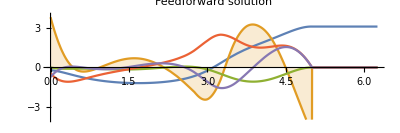

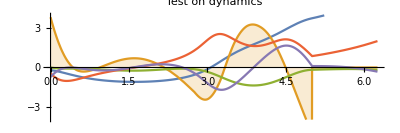

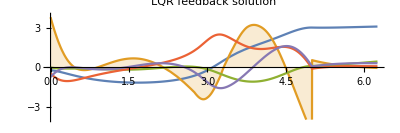

```mathematica
n=20;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;Weight = 0;
xdotMin = -2;
xdotMax = 2;
θMin = -π;
θMax = π;
θdotMin = -2;
θdotMax = 2;
xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit};
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};

{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,InitGuess,Weight]; 
k = 7/8;
ICs2 = {x1a[k*τ],xdot1a[k*τ],θ1a[k*τ],θdot1a[k*τ]};
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

Now Update the Initial Conditions to what were obtained at 3τ/4

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

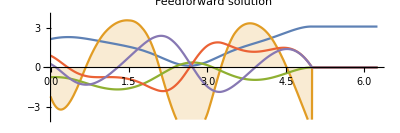

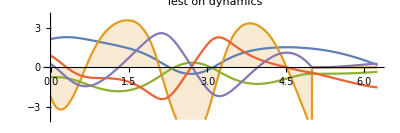

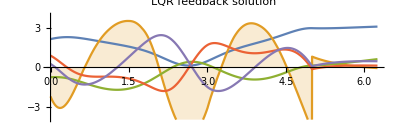

```mathematica
n=20;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;Weight = 0.3;
ICs = ICs2;
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,InitGuess,Weight]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

However if we put Weight = 0

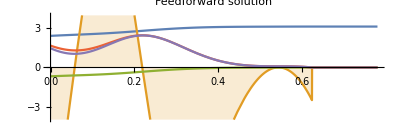

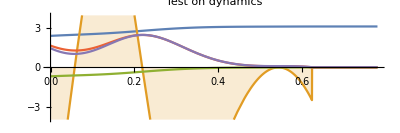

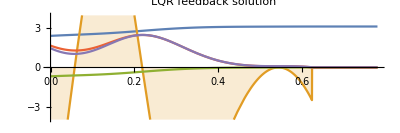

```mathematica
n=20;τ=5*(1-k);τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;Weight = 0;
ICs =ICs2;
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,InitGuess,Weight]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```